## Jednacine za sistem od 3 nivoa

```mathematica
H=({{0, Ω1, 0}, {Ω1, Δ1, Ω2}, {0, Ω2, Δ1+Δ2}});

ρ=({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}});

L=γ12/2(2*({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}).ρ.({{0, 0, 0}, {1, 0, 0}, {0, 0, 0}})-({{0, 0, 0}, {1, 0, 0}, {0, 0, 0}}).({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}}).ρ-ρ.({{0, 0, 0}, {1, 0, 0}, {0, 0, 0}}).({{0, 1, 0}, {0, 0, 0}, {0, 0, 0}})) + γ23/2(2*({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}).ρ.({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}})-({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}}).({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}).ρ-ρ.({{0, 0, 0}, {0, 0, 0}, {0, 1, 0}}).({{0, 0, 0}, {0, 0, 1}, {0, 0, 0}}));

dρdt=-ⅈ*(H.ρ-ρ.H)+L;
```

## Resavanje jednacina za sistem od 3 nivoa

```mathematica
Clear[Δ1]

γ12=1;
γ23=1;

(*Δ1=0;*)
Δ2=0;

Ω1=0.05;
Ω2=10;


S=Solve[{
γ12 ρ22-ⅈ (-ρ12 Ω1+ρ21 Ω1)==0,
-(γ12 ρ12)/2-ⅈ (-Δ1 ρ12-ρ11 Ω1+ρ22 Ω1-ρ13 Ω2)==0,
-(γ23 ρ13)/2-ⅈ (-(Δ1+Δ2) ρ13+ρ23 Ω1-ρ12 Ω2)==0,

-(γ12 ρ21)/2-ⅈ (Δ1 ρ21+ρ11 Ω1-ρ22 Ω1+ρ31 Ω2)==0,
-γ12 ρ22+γ23 ρ33-ⅈ (ρ12 Ω1-ρ21 Ω1-ρ23 Ω2+ρ32 Ω2)==0,
-(γ12 ρ23)/2-(γ23 ρ23)/2-ⅈ (Δ1 ρ23-(Δ1+Δ2) ρ23+ρ13 Ω1-ρ22 Ω2+ρ33 Ω2)==0,

-(γ23 ρ31)/2-ⅈ ((Δ1+Δ2) ρ31-ρ32 Ω1+ρ21 Ω2)==0,
-(γ12 ρ32)/2-(γ23 ρ32)/2-ⅈ (-Δ1 ρ32+(Δ1+Δ2) ρ32-ρ31 Ω1+ρ22 Ω2-ρ33 Ω2)==0,
-γ23 ρ33-ⅈ (ρ23 Ω2-ρ32 Ω2)==0,

ρ11+ρ22+ρ33==1

},
{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ρ33}][[1]];

ρ=({{S[[1,2]], S[[2,2]], S[[3,2]]}, {S[[4,2]], S[[5,2]], S[[6,2]]}, {S[[7,2]], S[[8,2]], S[[9,2]]}});
```

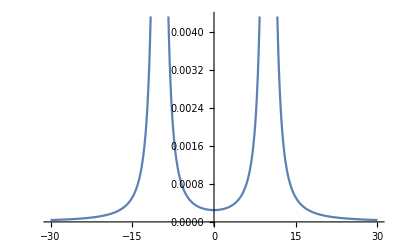

```mathematica
Plot[Im[ρ[[1,2]]],{Δ1,-30,30}]
```

## Plotovanje sa For

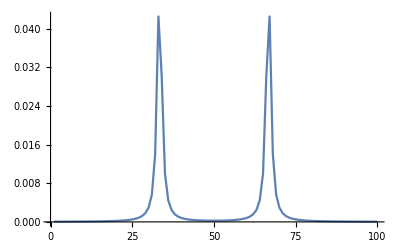

```mathematica
Imax=100;

For[i=1,i<=Imax,i++,

Δ1=-30+i*60/Imax;

γ12=1;
γ23=1;

Δ2=0;

Ω1=0.05;
Ω2=10;


S=Solve[{
γ12 ρ22-ⅈ (-ρ12 Ω1+ρ21 Ω1)==0,
-(γ12 ρ12)/2-ⅈ (-Δ1 ρ12-ρ11 Ω1+ρ22 Ω1-ρ13 Ω2)==0,
-(γ23 ρ13)/2-ⅈ (-(Δ1+Δ2) ρ13+ρ23 Ω1-ρ12 Ω2)==0,

-(γ12 ρ21)/2-ⅈ (Δ1 ρ21+ρ11 Ω1-ρ22 Ω1+ρ31 Ω2)==0,
-γ12 ρ22+γ23 ρ33-ⅈ (ρ12 Ω1-ρ21 Ω1-ρ23 Ω2+ρ32 Ω2)==0,
-(γ12 ρ23)/2-(γ23 ρ23)/2-ⅈ (Δ1 ρ23-(Δ1+Δ2) ρ23+ρ13 Ω1-ρ22 Ω2+ρ33 Ω2)==0,

-(γ23 ρ31)/2-ⅈ ((Δ1+Δ2) ρ31-ρ32 Ω1+ρ21 Ω2)==0,
-(γ12 ρ32)/2-(γ23 ρ32)/2-ⅈ (-Δ1 ρ32+(Δ1+Δ2) ρ32-ρ31 Ω1+ρ22 Ω2-ρ33 Ω2)==0,
-γ23 ρ33-ⅈ (ρ23 Ω2-ρ32 Ω2)==0,

ρ11+ρ22+ρ33==1

},
{ρ11,ρ12,ρ13,ρ21,ρ22,ρ23,ρ31,ρ32,ρ33}][[1]];

ρ=({{S[[1,2]], S[[2,2]], S[[3,2]]}, {S[[4,2]], S[[5,2]], S[[6,2]]}, {S[[7,2]], S[[8,2]], S[[9,2]]}});

a[i]=ρ[[1,2]];

]

ListLinePlot[Table[{n,Im[a[n]]},{n,Imax}],PlotRange->All]
```